Load approximation package

```mathematica
Needs["FunctionApproximations`"]
```

We want to approximate the function bd0(k,NP) = k log(k/NP) + NP -k and to do so we first transform to a more efficient version:
bd0(k,NP) = NP D_0(k /NP)  where D_0(ϵ) = ϵ log(ϵ) + 1 -ϵ. For ϵ close to 1 rather than evaluating D_0 directly we perform a series expansion. First we define v=(ϵ-1)/(ϵ+1) and then write
D_0(ϵ) = v (ϵ-1) + 2ϵ v ϕ_1(v)

Note then that ϕ_1(v) = Σ_(n=1)v^(2n)/(2n+3) . To accurately approximate this function define t=v^2  and find the minimax approximation in terms of t on some pre-defined interval.

```mathematica
Subscript[ϕ, 1][t_]:=-1+Log[-(1+√t)/(-1+√t)]/(2 √t)
```

It is hard to work with the exact form of ϕ_1 due to the removable pole at t=0. Instead consider the series expansion around t=0 up to arbitrary order.

```mathematica
Z[t_,n_]:=Normal[Series[Subscript[ϕ, 1][t],{t,0,n}]]
```

Now consider a rational minimax approximation of order (p,q) of the function R_m(t) = ϕ_1(t)  -Σ_(n=1)^m t^n/(2n+3) , i.e. the remainder of the truncated Taylor series.

```mathematica
m = 1;
p = 4;
q = 4;
tmax = 0.25;
minimax=MiniMaxApproximation[Normal[Series[(Subscript[ϕ, 1][t] - Z[t,m])/(t^(m+1)),{t,0,100}]],{t,{0,tmax},p,q},MaxIterations->100,WorkingPrecision->400][[2]];
poly[t_]:=Evaluate[ (Z[t,m]+t^(m+1)*minimax[[1]])]
minimax[[2]] (* minimax error *)
```

-3.391164822228570153033200051098049380470339932472299395610433929605662762218398949088399548719090404652331919538115202983318203338097800928739529130851105622134584839178401894218550453598155769529006869867450276105080300604211630582670052546586504350637763012180014618382590866412998914127731869418897554695584542632142993359331522308160820617992154796627398324892337184310911482297932552681675032103×10^-16

Define relative error of the minimax approximation to the original function and plot over range of allowed values to check whether it is of machine precision level

```mathematica
prec = $MachineEpsilon/2; (*double precision*)
(*prec = 2^-24;*)(*single precision*)
```

LogLogPlot::precw: The precision of the argument function ({9.0072×10^15 Abs[1-(Times[«2»]+Times[«3»])/Plus[«2»]]-0,-(1+√(ⅇ^(Charting`Private`pvar$1348)))/(-1+√(ⅇ^(Charting`Private`pvar$1348)))-0,ⅇ^(Charting`Private`pvar$1348)-0,(-1+Log[-(1+Power[«2»])/Plus[«2»]]/(2 √(ⅇ^(«26»))))-0,(-1+√(ⅇ^(Charting`Private`pvar$1348)))-0,(1-«431» ⅇ^(Charting`Private`pvar$1348)+«431» ⅇ^(2 Charting`Private`pvar$1348)-«431» ⅇ^(3 Charting`Private`pvar$1348)+«431» ⅇ^(4 Charting`Private`pvar$1348))-0,-Im[(1+√Power[«2»])/(-1+Power[«2»])]-0,Im[ⅇ^(Charting`Private`pvar$1348)]-0}) is less than WorkingPrecision (400.).

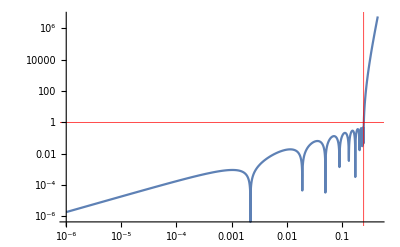

```mathematica
rerr[t_]:=Abs[1-poly[t]/Subscript[ϕ, 1][t]]
LogLogPlot[rerr[t]/prec,{t,10.^-6,tmax + 0.2},WorkingPrecision->400,PlotRange->All,GridLines->{{tmax},{1}},GridLinesStyle->Directive[Red,Thick]]
```

Check how the approximation performs in the overall approximation of rlog1(x)

```mathematica
D0[x_]:=x Log[x]+1-x
v[x_]:=(x-1)/(x+1)
P[x_]:=v[x]*(x-1+2 x*poly[v[x]^2])
```

Over what range of x is the approximation valid?

```mathematica
X=Sort[x/.Solve[t==((x-1)/(x+1))^2,x]/.{t->tmax}]
```

{0.333333,3.}

Red line indicates relative precision at machine precision level

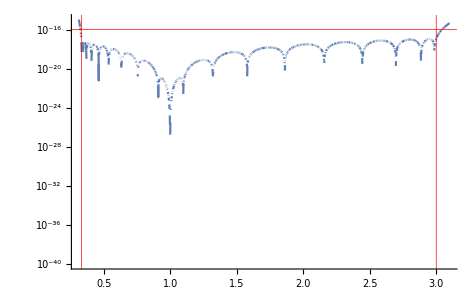

```mathematica
LogPlot[Abs[1-P[x]/D0[x]],{x,X[[1]]-0.1,X[[2]]+0.1},PlotRange->{All,{10^-40,10*prec}},WorkingPrecision->400,GridLines->{{X[[1]],X[[2]]},{prec}},GridLinesStyle->Directive[Red,Thick]]
```

Finally print out the approximation

```mathematica
N[poly[t],16]
```

0.3333333333333333 t+(t^2 (0.2000000000000001-0.3669101082562791 t+0.2056846557845579 t^2-0.03394955490410171 t^3+0.00005007384892489343 t^4))/(1.-2.54883625556692 t+2.293465048754533 t^2-0.8464624069944372 t^3+0.1046656636182324 t^4)